```mathematica
Clear[axk,ayk,k,ax,ay,bx,by,qx,qy]
```

#### Using the Bouwkamp definition for impedance; Power/v^2 Power emitted by the radiator at z=0 plane is the integral of p(x,y)*v(x,y) ds over x-y plane leads to the square of the fourier transform of the deflection profile in the integrand = S^2(kx,ax,bx) * S^2(ky,ay,by) where S(k,a,b) is 1D FT of one of the dimensions of the deflection profile - defined in the notes S(kx,ax,bx)/bx = xS below; q=a/b

```mathematica
xS=((-8/x)((1/(x^2) + 6/(x^4) + (2/5)*(SphericalBesselY[3,x]+SphericalBesselY[1,x]))*Sin[qx*x] + (-2/5)*(SphericalBesselJ[3,x] + SphericalBesselJ[1,x])*Cos[qx*x]))^2;
```

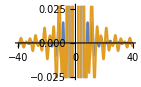
```mathematica
(*qx=1;
Plot[{xS[x,qx], 3.0671312295349495 Sinc[1.5355271144573683 x] Sinc[0.37611190490493007 x]},{x,-40,40}]*)
-Graphics-
(*
Clear[a,b,qx]
qx=1;
pnts=Table[{x,Re[xS[x,qx]]},{x,-5,5,0.015}]//N;
ListPlot[%]
FindFit[pnts,a Sinc[b x] Sinc[d x],{a,b,c,d},x]
(*
Table[{qx,FindFit[Table[Re[xS[x,qx]],{x,-5,5,0.015}]//N,a Sinc[b x],{a,b},x]},{qx,{1,2,3,4,5,6,7,8,9,10}}]*)*)
-Graphics-
{a->3.0671312295349495,b->1.5355271144573683,c->1.,d->0.37611190490493007}
```

Using the first identity listed here: https://dlmf.nist.gov/10.51
The following is equivalent to the expression above

```mathematica
xSs=(-8((1/(x^3) + 6/(x^5) + (2/5)*((1/3)SphericalBesselY[0,x]+(10/21)SphericalBesselY[2,x]+(1/7)SphericalBesselY[4,x]))*Sin[qx*x] + (-2/5)*((1/3)SphericalBesselJ[0,x]+(10/21)SphericalBesselJ[2,x]+(1/7)SphericalBesselJ[4,x])*Cos[qx*x]))^2;
(*qx=2;
NIntegrate[Abs[xS-xSs],{x,-50,50}]
Plot[{xS,xSs},{x,-5,5}]*)
```

64 (-2/5 Cos[qx x] (1/3 SphericalBesselJ[0,x]+10/21 SphericalBesselJ[2,x]+1/7 SphericalBesselJ[4,x])+Sin[qx x] (6/x^5+1/x^3+2/5 (1/3 SphericalBesselY[0,x]+10/21 SphericalBesselY[2,x]+1/7 SphericalBesselY[4,x])))^2

The impedance is then the integral of “S^2(kx,ax,bx) S^2(ky,ay,by) 1/kz dkx dky“ over kx and ky from -inf to inf
with the coefficient \frac{k\rho c v^2_0 }{4\pi^2} b^2_x b^2_y
	After change of variables the integrand will be: “S^2(k t cos(phi),ax,bx) S^2(k t sin(phi),ay,by) t dt dphi / sqrt(1-t^2)”
	with the coefficient: \frac{k^2 \rho c v^2_0 }{4\pi^2} b^2_x b^2_y * (1/V_ref)^2

```mathematica
xOrig=(-8((1/(x^3) + 6/(x^5) + (2/5)*((1/3)SphericalBesselY[0,x]+(10/21)SphericalBesselY[2,x]+(1/7)SphericalBesselY[4,x]))*Sin[qx*x] + (-2/5)*((1/3)SphericalBesselJ[0,x]+(10/21)SphericalBesselJ[2,x]+(1/7)SphericalBesselJ[4,x])*Cos[qx*x]))^2
xOrig=ReplaceAll[xOrig,x->(bxk*t*Cos[ϕ])];
yOrig=(-8((1/(x^3) + 6/(x^5) + (2/5)*((1/3)SphericalBesselY[0,x]+(10/21)SphericalBesselY[2,x]+(1/7)SphericalBesselY[4,x]))*Sin[qx*x] + (-2/5)*((1/3)SphericalBesselJ[0,x]+(10/21)SphericalBesselJ[2,x]+(1/7)SphericalBesselJ[4,x])*Cos[qx*x]))^2;
yOrig=ReplaceAll[yOrig,qx->qy];
yOrig=ReplaceAll[yOrig,x->(byk*t*Sin[ϕ])];
```

64 (-2/5 Cos[qx x] (1/3 SphericalBesselJ[0,x]+10/21 SphericalBesselJ[2,x]+1/7 SphericalBesselJ[4,x])+Sin[qx x] (6/x^5+1/x^3+2/5 (1/3 SphericalBesselY[0,x]+10/21 SphericalBesselY[2,x]+1/7 SphericalBesselY[4,x])))^2

```mathematica
Series[(-8((1/(x^3) + 6/(x^5) + (2/5)*((1/3)SphericalBesselY[0,x]+(10/21)SphericalBesselY[2,x]+(1/7)SphericalBesselY[4,x]))*Sin[qx*x] + (-2/5)*((1/3)SphericalBesselJ[0,x]+(10/21)SphericalBesselJ[2,x]+(1/7)SphericalBesselJ[4,x])*Cos[qx*x]))^2,{x,0,8}]
```

4/225 (8+15 qx)^2-(4 ((8+15 qx) (8+35 qx+56 qx^2+35 qx^3)) x^2)/1575+64 (((8+35 qx+56 qx^2+35 qx^3)^2)/705600+2 (-2/15-qx/4) (-qx/576-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))) x^4+64 (1/420 (8+35 qx+56 qx^2+35 qx^3) (-qx/576-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))+2 (-2/15-qx/4) (qx/28800+qx^3/3456+qx^5/2880+qx^7/20160-2/5 (-1/99792-qx^2/3024-qx^4/1008-qx^6/2160))) x^6+64 ((-qx/576-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))^2+1/420 (8+35 qx+56 qx^2+35 qx^3) (qx/28800+qx^3/3456+qx^5/2880+qx^7/20160-2/5 (-1/99792-qx^2/3024-qx^4/1008-qx^6/2160))+2 (-2/15-qx/4) (-qx/2419200-qx^3/172800-qx^5/69120-qx^7/120960-qx^9/1451520-2/5 (1/10378368+qx^2/199584+qx^4/36288+qx^6/30240+qx^8/120960))) x^8+O[x]^9

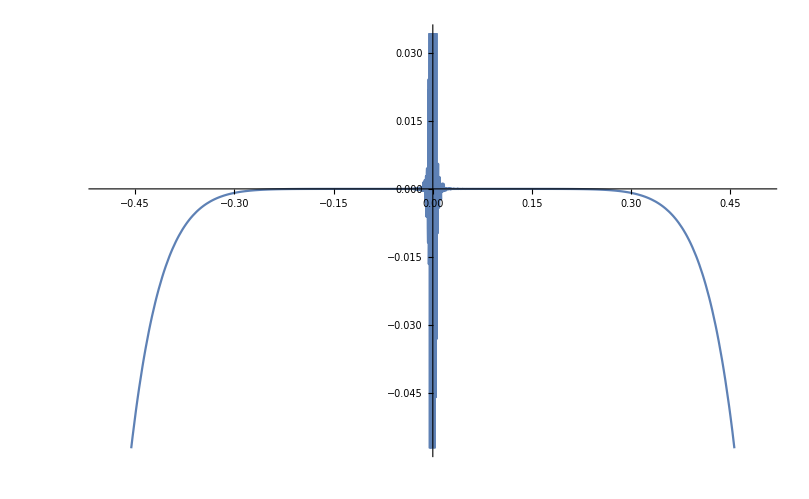

```mathematica
qx=2;
tempo=(-8((1/(x^3) + 6/(x^5) + (2/5)*((1/3)SphericalBesselY[0,x]+(10/21)SphericalBesselY[2,x]+(1/7)SphericalBesselY[4,x]))*Sin[qx*x] + (-2/5)*((1/3)SphericalBesselJ[0,x]+(10/21)SphericalBesselJ[2,x]+(1/7)SphericalBesselJ[4,x])*Cos[qx*x]))^2;
tempx=4/225 (8+15 qx)^2-(4 ((8+15 qx) (8+35 qx+56 qx^2+35 qx^3)) x^2)/1575+64 (((8+35 qx+56 qx^2+35 qx^3)^2)/705600+2 (-2/15-qx/4) (-qx/576-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))) x^4+64 (1/420 (8+35 qx+56 qx^2+35 qx^3) (-qx/576-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))+2 (-2/15-qx/4) (qx/28800+qx^3/3456+qx^5/2880+qx^7/20160-2/5 (-1/99792-qx^2/3024-qx^4/1008-qx^6/2160))) x^6+64 ((-qx/576-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))^2+1/420 (8+35 qx+56 qx^2+35 qx^3) (qx/28800+qx^3/3456+qx^5/2880+qx^7/20160-2/5 (-1/99792-qx^2/3024-qx^4/1008-qx^6/2160))+2 (-2/15-qx/4) (-qx/2419200-qx^3/172800-qx^5/69120-qx^7/120960-qx^9/1451520-2/5 (1/10378368+qx^2/199584+qx^4/36288+qx^6/30240+qx^8/120960))) x^8;
Plot[{100*tempo-100*tempx},{x,-0.5,0.5}]
```

```mathematica
xApprox=4/225 (8+15 qx)^2-(4 ((8+15 qx) (8+35 qx+56 qx^2+35 qx^3)) x^2)/1575+64 (((8+35 qx+56 qx^2+35 qx^3)^2)/705600+2 (-2/15-qx/4) (-qx/576-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))) x^4+64 (1/420 (8+35 qx+56 qx^2+35 qx^3) (-qx/576-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))+2 (-2/15-qx/4) (qx/28800+qx^3/3456+qx^5/2880+qx^7/20160-2/5 (-1/99792-qx^2/3024-qx^4/1008-qx^6/2160))) x^6+64 ((-qx/576-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))^2+1/420 (8+35 qx+56 qx^2+35 qx^3) (qx/28800+qx^3/3456+qx^5/2880+qx^7/20160-2/5 (-1/99792-qx^2/3024-qx^4/1008-qx^6/2160))+2 (-2/15-qx/4) (-qx/2419200-qx^3/172800-qx^5/69120-qx^7/120960-qx^9/1451520-2/5 (1/10378368+qx^2/199584+qx^4/36288+qx^6/30240+qx^8/120960))) x^8;
(*xApprox=ReplaceAll[xApprox,qx->(ax/bx)];*)
xApprox=ReplaceAll[xApprox,x->(bxk*t*Cos[ϕ])];

yApprox=4/225 (8+15 qx)^2-(4 ((8+15 qx) (8+35 qx+56 qx^2+35 qx^3)) x^2)/1575+64 (((8+35 qx+56 qx^2+35 qx^3)^2)/705600+2 (-2/15-qx/4) (-qx/576-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))) x^4+64 (1/420 (8+35 qx+56 qx^2+35 qx^3) (-qx/576-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))+2 (-2/15-qx/4) (qx/28800+qx^3/3456+qx^5/2880+qx^7/20160-2/5 (-1/99792-qx^2/3024-qx^4/1008-qx^6/2160))) x^6+64 ((-qx/576-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))^2+1/420 (8+35 qx+56 qx^2+35 qx^3) (qx/28800+qx^3/3456+qx^5/2880+qx^7/20160-2/5 (-1/99792-qx^2/3024-qx^4/1008-qx^6/2160))+2 (-2/15-qx/4) (-qx/2419200-qx^3/172800-qx^5/69120-qx^7/120960-qx^9/1451520-2/5 (1/10378368+qx^2/199584+qx^4/36288+qx^6/30240+qx^8/120960))) x^8;
(*yApprox=ReplaceAll[yApprox,qx->(ay/by)];*)
yApprox=ReplaceAll[yApprox,qx->qy];
yApprox=ReplaceAll[yApprox,x->(byk*t*Sin[ϕ])];
```

4/225 (8+15 qy)^2-(4 byk^2 (8+15 qy) (8+35 qy+56 qy^2+35 qy^3) t^2 Sin[ϕ]^2)/1575+64 byk^4 (((8+35 qy+56 qy^2+35 qy^3)^2)/705600+2 (-2/15-qy/4) (-qy/576-qy^3/144-qy^5/480-2/5 (1/1512+qy^2/84+qy^4/72))) t^4 Sin[ϕ]^4+64 byk^6 (1/420 (8+35 qy+56 qy^2+35 qy^3) (-qy/576-qy^3/144-qy^5/480-2/5 (1/1512+qy^2/84+qy^4/72))+2 (-2/15-qy/4) (qy/28800+qy^3/3456+qy^5/2880+qy^7/20160-2/5 (-1/99792-qy^2/3024-qy^4/1008-qy^6/2160))) t^6 Sin[ϕ]^6+64 byk^8 ((-qy/576-qy^3/144-qy^5/480-2/5 (1/1512+qy^2/84+qy^4/72))^2+1/420 (8+35 qy+56 qy^2+35 qy^3) (qy/28800+qy^3/3456+qy^5/2880+qy^7/20160-2/5 (-1/99792-qy^2/3024-qy^4/1008-qy^6/2160))+2 (-2/15-qy/4) (-qy/2419200-qy^3/172800-qy^5/69120-qy^7/120960-qy^9/1451520-2/5 (1/10378368+qy^2/199584+qy^4/36288+qy^6/30240+qy^8/120960))) t^8 Sin[ϕ]^8

```mathematica
(*axk=1;
ayk=1;
ax=0.003;
ay=0.003;
k=axk/ax;
bx=0.5/k;
by=0.5/k;*)
```

```mathematica
xComplete=Piecewise[{{xApprox,Abs[bxk t Cos[ϕ]]<0.1}},xOrig];
yComplete=Piecewise[{{yApprox,Abs[byk t Sin[ϕ]]<0.1}},yOrig];
```

```mathematica
3600 k^2 *(((ax+bx)^2)/(15 ax+8 bx))*(((ay+by)^2)/(15 ay+8 by))*(Pi^(-2)) NIntegrate[(t/Sqrt[1-t^2])*xPart*yPart,{t,0,1},{ϕ,0,2 Pi}]
```

0.93257

```mathematica
Plot3D[(t/Sqrt[1-t^2])*xPart*yPart,{t,0,1},{ϕ,0,Pi/2},PlotStyle->Directive[RGBColor[0.92,0.96,0.96],Opacity[0.85]],Mesh->All,MeshFunctions->Automatic]
```

-Graphics3D-

### Reactance

```mathematica
-3600 k^2 *(((ax+bx)^2)/(15 ax+8 bx))*(((ay+by)^2)/(15 ay+8 by))*(Pi^(-2)) NIntegrate[(t/Sqrt[t^2-1])*xPart*yPart,{t,1,∞},{ϕ,0,2 Pi}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-0.722398

### Coding with Mathematica

```mathematica
Clear[axk,ayk,k,ax,ay,bx,by,qx,qy]
```

```mathematica
xOriginal[bxk_,qx_]:=64 (-(2/5) Cos[bxk qx t Cos[ϕ]] (1/3 SphericalBesselJ[0,bxk t Cos[ϕ]]+10/21 SphericalBesselJ[2,bxk t Cos[ϕ]]+1/7 SphericalBesselJ[4,bxk t Cos[ϕ]])+Sin[bxk qx t Cos[ϕ]] (Sec[ϕ]^3/(bxk^3 t^3)+(6 Sec[ϕ]^5)/(bxk^5 t^5)+2/5 (1/3 SphericalBesselY[0,bxk t Cos[ϕ]]+10/21 SphericalBesselY[2,bxk t Cos[ϕ]]+1/7 SphericalBesselY[4,bxk t Cos[ϕ]])))^2
yOriginal[byk_,qy_]:=64 (-(2/5) Cos[byk qy t Sin[ϕ]] (1/3 SphericalBesselJ[0,byk t Sin[ϕ]]+10/21 SphericalBesselJ[2,byk t Sin[ϕ]]+1/7 SphericalBesselJ[4,byk t Sin[ϕ]])+Sin[byk qy t Sin[ϕ]] (Csc[ϕ]^3/(byk^3 t^3)+(6 Csc[ϕ]^5)/(byk^5 t^5)+2/5 (1/3 SphericalBesselY[0,byk t Sin[ϕ]]+10/21 SphericalBesselY[2,byk t Sin[ϕ]]+1/7 SphericalBesselY[4,byk t Sin[ϕ]])))^2
xApproximate[bxk_,qx_]:=4/225 (8+15 qx)^2-(4 bxk^2 (8+15 qx) (8+35 qx+56 qx^2+35 qx^3) t^2 Cos[ϕ]^2)/1575+64 bxk^4 ((8+35 qx+56 qx^2+35 qx^3)^2/705600+2 (-(2/15)-qx/4) (-(qx/576)-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))) t^4 Cos[ϕ]^4+64 bxk^6 (1/420 (8+35 qx+56 qx^2+35 qx^3) (-(qx/576)-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))+2 (-(2/15)-qx/4) (qx/28800+qx^3/3456+qx^5/2880+qx^7/20160-2/5 (-(1/99792)-qx^2/3024-qx^4/1008-qx^6/2160))) t^6 Cos[ϕ]^6+64 bxk^8 ((-(qx/576)-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))^2+1/420 (8+35 qx+56 qx^2+35 qx^3) (qx/28800+qx^3/3456+qx^5/2880+qx^7/20160-2/5 (-(1/99792)-qx^2/3024-qx^4/1008-qx^6/2160))+2 (-(2/15)-qx/4) (-(qx/2419200)-qx^3/172800-qx^5/69120-qx^7/120960-qx^9/1451520-2/5 (1/10378368+qx^2/199584+qx^4/36288+qx^6/30240+qx^8/120960))) t^8 Cos[ϕ]^8
yApproximate[byk_,qy_]:=4/225 (8+15 qy)^2-(4 byk^2 (8+15 qy) (8+35 qy+56 qy^2+35 qy^3) t^2 Sin[ϕ]^2)/1575+64 byk^4 ((8+35 qy+56 qy^2+35 qy^3)^2/705600+2 (-(2/15)-qy/4) (-(qy/576)-qy^3/144-qy^5/480-2/5 (1/1512+qy^2/84+qy^4/72))) t^4 Sin[ϕ]^4+64 byk^6 (1/420 (8+35 qy+56 qy^2+35 qy^3) (-(qy/576)-qy^3/144-qy^5/480-2/5 (1/1512+qy^2/84+qy^4/72))+2 (-(2/15)-qy/4) (qy/28800+qy^3/3456+qy^5/2880+qy^7/20160-2/5 (-(1/99792)-qy^2/3024-qy^4/1008-qy^6/2160))) t^6 Sin[ϕ]^6+64 byk^8 ((-(qy/576)-qy^3/144-qy^5/480-2/5 (1/1512+qy^2/84+qy^4/72))^2+1/420 (8+35 qy+56 qy^2+35 qy^3) (qy/28800+qy^3/3456+qy^5/2880+qy^7/20160-2/5 (-(1/99792)-qy^2/3024-qy^4/1008-qy^6/2160))+2 (-(2/15)-qy/4) (-(qy/2419200)-qy^3/172800-qy^5/69120-qy^7/120960-qy^9/1451520-2/5 (1/10378368+qy^2/199584+qy^4/36288+qy^6/30240+qy^8/120960))) t^8 Sin[ϕ]^8
```

```mathematica
xPartInt[bxk_,qx_]:=Piecewise[{{xApproximate[bxk,qx],Abs[bxk t Cos[ϕ]]<0.1}},xOriginal[bxk,qx]]
yPartInt[byk_,qy_]:=Piecewise[{{yApproximate[byk,qy],Abs[byk t Sin[ϕ]]<0.1}},yOriginal[byk,qy]]
```

```mathematica
zR[bxk_,qx_,qxy_,qy_]:=bxk^2 (bxk*qx/(qxy*qy))^2 /(4 (315 qx bxk+128 bxk) (315 (bxk*qx/qxy)+128 (bxk*qx/(qxy*qy)))/99225) ((4 Pi^2)^(-1)) (*Normalized as P_tot/(ρ c v_R^2 S_0)*)NIntegrate[(t/Sqrt[1-t^2])*xPartInt[bxk,qx]*yPartInt[bxk*qx/(qxy*qy),qy],{t,0,1},{ϕ,0,2Pi}];zI[bxk_,qx_,qxy_,qy_]:=bxk^2 (bxk*qx/(qxy*qy))^2/(4 (315 qx bxk+128 bxk) (315 (bxk*qx/qxy)+128 (bxk*qx/(qxy*qy)))/99225) ((4 Pi^2)^(-1)) NIntegrate[(t/Sqrt[t^2-1])*xPartInt[bxk,qx]*yPartInt[bxk*qx/(qxy*qy),qy],{t,1,∞},{ϕ,0,2Pi}];
```

Example of a calculation:
After running the cells below “Coding with Mathematica”, run the cell below as the example.

```mathematica
Monitor[Table[{10^i,j,r,j,zR[10^i,j,r,j],zI[10^i,j,r,j]},{i,{-1.5,-1.4,-1.3,-1.2,-1.1,-0.9,-0.8,-0.6,-0.4,-0.3,-0.1}},{j,{1,5}},{r,{1,1/3,0.1,0.04}}],i]
dat=%;
Export["temp_j1_j5.txt",dat,"Table","FieldSeparators"->","]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ϕ near {t,ϕ} = {0.844124,3.22008×10^-6}. NIntegrate obtained 56849.9 and 8.85782 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ϕ near {t,ϕ} = {0.844124,7.03477×10^-6}. NIntegrate obtained 25189. and 0.318967 for the integral and error estimates.

NIntegrate::zeroregion: Integration region {{1.,1.},{0.0941107,0.392699}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ϕ near {t,ϕ} = {0.844124,3.22008×10^-6}. NIntegrate obtained 19991.4 and 1.10952 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::zeroregion: Integration region {{1.,1.},{6.26917616275159379594927866463649479555897414684295654296875,6.18907456524075323678335536214945022948086261749267578125}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::zeroregion: Integration region {{1.,1.},{0.0140091,0.0941107}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

General::stop: Further output of NIntegrate::zeroregion will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6294.36 and 0.00851995 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3893.45 and 0.00552468 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1132.21 and 0.0024432 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{{{{0.0316228,1,1,1,0.00177828,0.0524628},{0.0316228,1,1/3,1,0.00532301,0.0842458},{0.0316228,1,0.1,1,0.0173041,0.120741},{0.0316228,1,0.04,1,0.0376675,0.138374}},{{0.0316228,5,1,5,0.0202792,0.170875},{0.0316228,5,1/3,5,0.0592066,0.266932},{0.0316228,5,0.1,5,0.148583,0.318695},{0.0316228,5,0.04,5,0.167651,0.307923}}},{{{0.0398107,1,1,1,0.00281746,0.0660127},{0.0398107,1,1/3,1,0.00842274,0.105842},{0.0398107,1,0.1,1,0.0269869,0.14993},{0.0398107,1,0.04,1,0.0545536,0.165089}},{{0.0398107,5,1,5,0.0320121,0.213761},{0.0398107,5,1/3,5,0.0920028,0.327862},{0.0398107,5,0.1,5,0.200971,0.360624},{0.0398107,5,0.04,5,0.216233,0.352017}}},{{{0.0501187,1,1,1,0.00446308,0.0830372},{0.0501187,1,1/3,1,0.0133149,0.132817},{0.0501187,1,0.1,1,0.0417038,0.184764},{0.0501187,1,0.04,1,0.0757952,0.193445}},{{0.0501187,5,1,5,0.0504153,0.266418},{0.0501187,5,1/3,5,0.141361,0.397089},{0.0501187,5,0.1,5,0.258582,0.401852},{0.0501187,5,0.04,5,0.271991,0.398404}}},{{{0.0630957,1,1,1,0.00706774,0.104402},{0.0630957,1,1/3,1,0.0210171,0.166352},{0.0630957,1,0.1,1,0.0635428,0.225113},{0.0630957,1,0.04,1,0.100288,0.223506}},{{0.0630957,5,1,5,0.0791048,0.330094},{0.0630957,5,1/3,5,0.213431,0.47065},{0.0630957,5,0.1,5,0.323825,0.448845},{0.0630957,5,0.04,5,0.344638,0.445602}}},{{{0.0794328,1,1,1,0.0111872,0.131165},{0.0794328,1,1/3,1,0.0330964,0.207733},{0.0794328,1,0.1,1,0.0947738,0.269804},{0.0794328,1,0.04,1,0.127472,0.257673}},{{0.0794328,5,1,5,0.123394,0.405164},{0.0794328,5,1/3,5,0.313756,0.539953},{0.0794328,5,0.1,5,0.410932,0.50009},{0.0794328,5,0.04,5,0.430807,0.48939}}},{{{0.125893,1,1,1,0.0279526,0.20614},{0.125893,1,1/3,1,0.0809844,0.318541},{0.125893,1,0.1,1,0.189862,0.361315},{0.125893,1,0.04,1,0.206152,0.344281}},{{0.125893,5,1,5,0.290421,0.578336},{0.125893,5,1/3,5,0.592874,0.607491},{0.125893,5,0.1,5,0.640494,0.551938},{0.125893,5,0.04,5,0.656254,0.540336}}},{{{0.158489,1,1,1,0.0440746,0.257398},{0.158489,1,1/3,1,0.125152,0.388482},{0.158489,1,0.1,1,0.250221,0.403485},{0.158489,1,0.04,1,0.260996,0.389334}},{{0.158489,5,1,5,0.432133,0.656824},{0.158489,5,1/3,5,0.740961,0.583008},{0.158489,5,0.1,5,0.781437,0.543858},{0.158489,5,0.04,5,0.790427,0.52972}}},{{{0.251189,1,1,1,0.108404,0.394455},{0.251189,1,1/3,1,0.284152,0.542448},{0.251189,1,0.1,1,0.396134,0.495788},{0.251189,1,0.04,1,0.409105,0.482471}},{{0.251189,5,1,5,0.839884,0.673384},{0.251189,5,1/3,5,0.996983,0.460517},{0.251189,5,0.1,5,1.04162,0.402484},{0.251189,5,0.04,5,1.04388,0.386935}}},{{{0.398107,1,1,1,0.258297,0.574169},{0.398107,1,1/3,1,0.563625,0.642248},{0.398107,1,0.1,1,0.622084,0.560131},{0.398107,1,0.04,1,0.62372,0.548061}},{{0.398107,5,1,5,1.1406,0.32841},{0.398107,5,1/3,5,1.10227,0.172545},{0.398107,5,0.1,5,1.10759,0.131089},{0.398107,5,0.04,5,1.10198,0.123531}}},{{{0.501187,1,1,1,0.388953,0.6649},{0.501187,1,1/3,1,0.728604,0.633034},{0.501187,1,0.1,1,0.756264,0.562904},{0.501187,1,0.04,1,0.75613,0.551579}},{{0.501187,5,1,5,1.07636,0.14538},{0.501187,5,1/3,5,1.04987,0.0953814},{0.501187,5,0.1,5,1.03569,0.057921},{0.501187,5,0.04,5,1.02995,0.054881}}},{{{0.794328,1,1,1,0.793573,0.741534},{0.794328,1,1/3,1,1.0139,0.505808},{0.794328,1,0.1,1,1.03385,0.451101},{0.794328,1,0.04,1,1.03097,0.445446}},{{0.794328,5,1,5,1.01919,0.192053},{0.794328,5,1/3,5,1.02707,0.11229},{0.794328,5,0.1,5,1.02235,0.0980388},{0.794328,5,0.04,5,1.02097,0.0977538}}}}

temp_j1_j5.txt